```mathematica
Clear["Global`*"]
```

1 - 6 Mixing problems.

1. Find out, without calculation, whether doubling the flow rate in example 1 has the same effect as halfing the tank sizes. (Give a reason.)

I see the answer to this problem is yes, which surprised me.

3. Derive the eigenvectors in example 1 without consulting this book.

```mathematica
A=({{-0.02, 0.02}, {0.02, -0.02}})
```

{{-0.02,0.02},{0.02,-0.02}}

```mathematica
Eigensystem[A]
```

{{-0.04,0.},{{0.707107,-0.707107},{0.707107,0.707107}}}

As there is no text answer to this problem, I can’t determine whether my guess is right or wrong.

5. If you extend example 1, p. 130 by a tank T_3 of the same size as the others, and connected to T_2 by two tubes with flow rates as between T_1 and T_2, what system of ODEs will you get?

The example in the text is basically the diagram below, except only the first two tanks. Working first with the example conditions,

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn1=Subscript[y, 1]'[x]==-0.02 Subscript[y, 1][x]+0.02 Subscript[y, 2][x];
eqn2=Subscript[y, 2]'[x]==0.02 Subscript[y, 1][x]-0.02 Subscript[y, 2][x];
ics={Subscript[y, 1][0]==0,Subscript[y, 2][0]==150};
```

The first DSolve will be to get a general solution of the system.

```mathematica
sol=DSolve[{eqn1,eqn2},{Subscript[y, 1],Subscript[y, 2]},x]
```

{{y_1→Function[{x},0.5 ⅇ^(-0.04 x) (1.+1. ⅇ^(0.04 x)) C[1]+0.5 ⅇ^(-0.04 x) (-1.+1. ⅇ^(0.04 x)) C[2]],y_2→Function[{x},0.5 ⅇ^(-0.04 x) (-1.+1. ⅇ^(0.04 x)) C[1]+0.5 ⅇ^(-0.04 x) (1.+1. ⅇ^(0.04 x)) C[2]]}}

The solution checks.

```mathematica
Chop[Simplify[eqn1/.sol],10^-17]
```

{True}

```mathematica
Chop[Simplify[eqn2/.sol],10^-17]
```

{True}

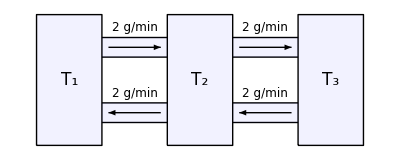

```mathematica
Graphics[{{Opacity[0.05],Blue,Rectangle[{0.5,0.5},{1.5,2.5}]},{Opacity[0.05],Blue,Rectangle[{2.5,0.5},{3.5,2.5}]},{Opacity[0.05],Blue,Rectangle[{4.5,0.5},{5.5,2.5}]},{Line[{{0.5,0.5},{1.5,0.5},{1.5,2.5},{0.5,2.5},{0.5,0.5}}]},{Line[{{2.5,0.5},{3.5,0.5},{3.5,2.5},{2.5,2.5},{2.5,0.5}}]},{Line[{{4.5,0.5},{5.5,0.5},{5.5,2.5},{4.5,2.5},{4.5,0.5}}]},{Line[{{1.5,0.85},{2.5,0.85}}]},{Line[{{1.5,1.15},{2.5,1.15}}]},{Opacity[0.05],Blue,Rectangle[{1.5,0.85},{2.5,1.15}]},{Line[{{1.5,1.85},{2.5,1.85}}]},{Line[{{1.5,2.15},{2.5,2.15}}]},{Opacity[0.05],Blue,Rectangle[{1.5,1.85},{2.5,2.15}]},{Line[{{3.5,0.85},{4.5,0.85}}]},{Line[{{3.5,1.15},{4.5,1.15}}]},{Opacity[0.05],Blue,Rectangle[{3.5,0.85},{4.5,1.15}]},{Line[{{3.5,1.85},{4.5,1.85}}]},{Line[{{3.5,2.15},{4.5,2.15}}]},{Opacity[0.05],Blue,Rectangle[{3.5,1.85},{4.5,2.15}]},{Text[Style[Subscript[T, 1],17],{1,1.5}]},{Text[Style[Subscript[T, 2],17],{3,1.5}]},{Text[Style[Subscript[T, 3],17],{5,1.5}]},{Text[Style["2 g/min",12],{2,2.3}]},{Text[Style["2 g/min",12],{2,1.3}]},{Text[Style["2 g/min",12],{4,2.3}]},{Text[Style["2 g/min",12],{4,1.3}]},{Arrow[{{2.4,1},{1.6,1}}]},{Arrow[{{4.4,1},{3.6,1}}]},{Arrow[{{1.6,2},{2.4,2}}]},{Arrow[{{3.6,2},{4.4,2}}]}},Axes->False]
```

Still working with the text example, in which there are two tanks, I can solve for the initial conditions, in which all 150 pounds of fertilizer starts out in tank T_2.

```mathematica
sol2=DSolve[{eqn1,eqn2,ics},{Subscript[y, 1],Subscript[y, 2]},x]
```

{{y_1→Function[{x},75. ⅇ^(-0.04 x) (-1.+1. ⅇ^(0.04 x))],y_2→Function[{x},75. ⅇ^(-0.04 x) (1.+1. ⅇ^(0.04 x))]}}

The question posed by the example is the time required for the first tank, T_1, to accumulate at least half the fertilizer that is in tank T_2. That will happen when T_1 has 50 pounds and T_2 has 100 pounds.

```mathematica
Solve[74.99999999999999 ⅇ^(-0.04 x) (-1.+1. ⅇ^(0.04 x))==50,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→27.4653}}

```mathematica
Solve[75. ⅇ^(-0.04 x) (1.+1. ⅇ^(0.04 x))==100,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→27.4653}}

The above answers match the text example pretty well. (The example gives 27.5 minutes as the time, and displays it on a graph, figure 78, p. 131.) Now, what will the system of ODEs look like with the addition of tank T_3? It is still just the circulation in and out, for each tank. Tank T_1 remains unchanged, its circulation limited to T_2. The circulation in tank T_2 will double, since it will have 4 gpm in and 4 gpm out. The outflow can be described as 2 y_2.  And there will be 2 gpm going to T_1, as well as 2 gpm going to T_3.

So altogether the equation for T_2 will be y_2'=0.02(y_1-2 y_2+y_3). As for T_(3,)it will be just like T_1, except on the other side of T_2, thus y_3'=0.02(y_2-y_3). This identification of the system of equations is all the problem description asks for.

But let me work it out. Suppose the 150 lbs of fertilzer starts out in T_2 as before, and it is desired to know when T_1 and T_2 have accumulated 25 pounds of fertilizer (which I think should be at the same time.)

```mathematica
eqn3=Subscript[y, 1]'[x]==-0.02 Subscript[y, 1][x]+0.02 Subscript[y, 2][x];
eqn4=Subscript[y, 2]'[x]==0.02 Subscript[y, 1][x]-2(0.02 Subscript[y, 2][x])+0.02 Subscript[y, 3][x];
eqn5=Subscript[y, 3]'[x]==-0.02 Subscript[y, 3][x]+0.02 Subscript[y, 2][x];
```

Mathematica is capable of solving the 3-equation problem, and the answer checks.

```mathematica
sol3=DSolve[{eqn3,eqn4,eqn5},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]},x];
```

```mathematica
Chop[Simplify[eqn3/.sol3],10^-17]
```

{True}

```mathematica
Chop[Simplify[eqn4/.sol3],10^-17]
```

{True}

```mathematica
Chop[Simplify[eqn5/.sol3],10^-17]
```

{True}

In the revised set of initial conditions, the 150 pounds of fertilizer is still deposited in T_2.

```mathematica
ics2={Subscript[y, 1][0]==0,Subscript[y, 2][0]==150,Subscript[y, 3][0]==0};
```

```mathematica
sol4=DSolve[{eqn3,eqn4,eqn5,ics2},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]},x]
```

{{y_1→Function[{x},50. ⅇ^(-0.08 x) (-1. ⅇ^(0.02 x)+6.73463×10^-18 ⅇ^(0.06 x)+1. ⅇ^(0.08 x))],y_2→Function[{x},50. ⅇ^(-0.08 x) (2. ⅇ^(0.02 x)-7.47694×10^-34 ⅇ^(0.06 x)+1. ⅇ^(0.08 x))],y_3→Function[{x},50. ⅇ^(-0.08 x) (-1. ⅇ^(0.02 x)-6.73463×10^-18 ⅇ^(0.06 x)+1. ⅇ^(0.08 x))]}}

And the time in minutes to get half of the fertilizer into the two auxillary tanks is sought.

```mathematica
Solve[50.00000000000001 ⅇ^(-0.08000000000000002 x) (-1. ⅇ^(0.020000000000000004 x)+6.7346319387675736*^-18 ⅇ^(0.06000000000000001 x)+1. ⅇ^(0.08000000000000002 x))==25,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→11.5525}}

```mathematica
Solve[50.00000000000002 ⅇ^(-0.08000000000000002 x) (1.999999999999999 ⅇ^(0.020000000000000004 x)-7.476943440795785*^-34 ⅇ^(0.06000000000000001 x)+1. ⅇ^(0.08000000000000002 x))==100,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→11.5525}}

```mathematica
Solve[50.00000000000002 ⅇ^(-0.08000000000000002 x) (-1. ⅇ^(0.020000000000000004 x)-6.734631938767571*^-18 ⅇ^(0.06000000000000001 x)+1. ⅇ^(0.08000000000000002 x))==25,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→11.5525}}

The above cells show that with the circulation doubled, the time to distribute one third of the fertilizer out of tank T_2 is much reduced, in fact by

```mathematica
1-11.552453009332412/27.465307216702744
```

0.57938

more than 50 percent.

7 - 9 Electrical network
In example 2, find the currents:

7. If the initial currents are 0 A and -3 A (minus meaning the I_2(0) flows against the direction of the arrow).

```mathematica
ClearAll["Global`*"]
```

In example 2 the applicable matrix is found as

```mathematica
({{-4, 4}, {-1.6, 1.2}})
```

{{-4,4},{-1.6,1.2}}

Mathematica , in calculating eigenvectors, always normalizes any which have any entries, in the parent matrix, which are floats. In this case I can pull the following into agreement with the text (which does not normalize the eigenvectors here) by rationalizing.

```mathematica
Rationalize[-1.6]
```

-8/5

```mathematica
Rationalize[1.2]
```

6/5

```mathematica
A=({{-4, 4}, {-8/5, 6/5}})
```

{{-4,4},{-8/5,6/5}}

For which the applicable eigenvalues and eigenvectors can be found as

```mathematica
{vals,vecs}=Eigensystem[A]
```

{{-2,-4/5},{{2,1},{5/4,1}}}

which I can then decimalize

```mathematica
NumberForm[N[{vals,vecs}],3]
```

{{-2.,-0.8},{{2.,1.},{1.25,1.}}}

Scooping up at a later stage in the example, there will be two equations for the two circuit loops. 

I_1=2 c_1 ⅇ^(-2t)+c_2 ⅇ^(-0.8t)+3  and I_2=c_1 ⅇ^(-2t)+0.8 c_2 ⅇ^(-0.8t)

For the case where t=0, the example, at top of p. 134, states these as

I_1[0]=2 c_1+c_2+3=0  and I_2[0]=c_1+0.8 c_2=-3

The alteration, from example 2, for this problem is that at t=0 the two current values are 0 and -3 Amp respectively, so the above equations can be solved by

```mathematica
Solve[2 Subscript[c, 1]+Subscript[c, 2]+3==0&&Subscript[c, 1]+0.8 Subscript[c, 2]==-3,{Subscript[c, 1],Subscript[c, 2]}]
```

{{c_1→1.,c_2→-5.}}

Then I will have

```mathematica
Subscript[I, 1][t]=(2 Subscript[c, 1] ⅇ^(-2t)+Subscript[c, 2] ⅇ^(-0.8t)+3 )/. {Subscript[c, 1]->0.9999999999999997,Subscript[c, 2]->-4.999999999999999}
```

3+2. ⅇ^(-2 t)-5. ⅇ^(-0.8 t)

and

```mathematica
Subscript[I, 2][t]=Subscript[c, 1] ⅇ^(-2t)+0.8 Subscript[c, 2] ⅇ^(-0.8t)/. {Subscript[c, 1]->0.9999999999999997,Subscript[c, 2]->-4.999999999999999}
```

1. ⅇ^(-2 t)-4. ⅇ^(-0.8 t)

The text answer only encompasses the constant values in green above, not the actual resulting current equations.

9. If the initial currents in example 2 are 28 A and 14 A.

The use of example 2 on p. 132 is not finished, there is this additional problem concerning it. Using the last problem, and jumping down to the pertinent expressions

```mathematica
Solve[2 Subscript[c, 1]+Subscript[c, 2]+3==28&&Subscript[c, 1]+0.8 Subscript[c, 2]==14,{Subscript[c, 1],Subscript[c, 2]}]
```

{{c_1→10.,c_2→5.}}

The above green cell matches the text answer. The text answer skips the final equations, so I will also.

10 - 13 Conversion to systems
Find a general solution of the given ODE (a) by first converting it to a system, (b), as given.

11.  4 y'' - 15 y' - 4 y = 0

(a) Convert to a system. Conversion to a system seems like it would be useful in some cases. However, as long as DSolve can get it done with such conversion, it is a little difficult to get motivated about it.

(b) As given

```mathematica
eqn=4y''[x]-15y'[x]-4y[x]==0
```

-4 y[x]-15 y'[x]+4 y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},ⅇ^(-x/4) C[1]+ⅇ^(4 x) C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

The answer in yellow above is correct, but not listed in the text answer. Instead, the text answer includes a vector of constants, which I think are ultimately absorbed by the constants shown above.

13.  y'' + 2 y' - 24 y = 0

```mathematica
ClearAll["Global`*"]
```

(b) As given

```mathematica
eqn=y''[x]+2y'[x]-24y[x]==0
```

-24 y[x]+2 y'[x]+y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},ⅇ^(-6 x) C[1]+ⅇ^(4 x) C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

The answer in green above matches the answer in the text.

15. CAS experiment. Electrical network.
(a) In Example 2, p. 132, choose a sequence of values of C that increases beyond bound, and compare the corresponding sequences of eigenvalues of A. What limits of these sequences do your numeric values (approximately) suggest?
(b) Find these limits analytically.
(c) Explain your result physically.
(d) Below what value (approximately) must you decrease C to get vibrations?